# Essentials of Programming in Mathematica

## Ch.1: Programming With Mathematica

## Exercises

1. Generate a random number between one and one hundred. Then create a vector of twelve random numbers between one and one hundred. Finally create a 4x4 array of such numbers and then compute the determinant of that array.

```mathematica
RandomReal[{1,100},{4,4}]//Det
```

1.81789×10^7

2. Using Table, create a 4x4 Hilbert matrix. The entry aij in row i, column j of the Hilbert matrix is given by . Check your solution against the built-in HilbertMatrix.

```mathematica
Table[1/(i+j-1),{i,1,4},{j,1,4}]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

```mathematica
HilbertMatrix[4]//MatrixForm
```

(1 | 1/2 | 1/3 | 1/4
1/2 | 1/3 | 1/4 | 1/5
1/3 | 1/4 | 1/5 | 1/6
1/4 | 1/5 | 1/6 | 1/7)

```mathematica
%5==%6
```

True

3. Add the two lists, {1, 2, 3, 4, 5} and {2, 4, 6, 8, 10}. Then multiply them element-wise. Finally, multiply the two lists as vectors (dot product).

```mathematica
{1,2,3,4,5}+{2,4,6,8,10}
{1,2,3,4,5}*{2,4,6,8,10}
{1,2,3,4,5}.{2,4,6,8,10}
```

{3,6,9,12,15}

{2,8,18,32,50}

110

4. Generate a list of the first 25 integers in five different ways.

```mathematica
Table[i,{i,1,25}]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
Range[1,25]
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
doList={};
Do[AppendTo[doList,i],{i,1,25}];
doList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
forList={};
For[i=1,i≤ 25,i++,AppendTo[forList,i]];
forList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

```mathematica
whileList={};
i=1;
While[i≤ 25,AppendTo[whileList,i];i++];
whileList
```

{1,2,3,4,5,6,7,8,9,10,11,12,13,14,15,16,17,18,19,20,21,22,23,24,25}

5. Add the integers one through one thousand in as many different ways as you can.

```mathematica
Sum[i,{i,1,1000}]
```

500500

```mathematica
ParallelSum[i,{i,1,1000}]
```

Updating from Wolfram Research server ...

Updating from Wolfram Research server ...

500500

```mathematica
Total[Range[1,1000]]
```

500500

```mathematica
Total[Table[i,{i,1,1000}]]
```

500500

```mathematica
i=0;
Do[i=i+j,{j,1,1000}];
i
```

500500

6. A 2×2 matrix can be created using lists such as {{a,b},{c,d}}. Deﬁne a 2×2 numerical matrix and then ﬁnd its inverse, determinant, transpose, and trace.

```mathematica
RandomReal[{0,1},{2,2}]//MatrixForm
```

(0.770901 | 0.772621
0.576254 | 0.497387)

```mathematica
Inverse[%18]//MatrixForm
```

(-8.04975 | 12.5042
9.32613 | -12.4763)

```mathematica
Det[%18]
```

-0.0617891

```mathematica
Transpose[%18]//MatrixForm
```

(0.770901 | 0.576254
0.772621 | 0.497387)

```mathematica
Tr[%18]
```

1.26829

## Ch.2: The Mathematica Language

## Examples

Random walk. Note that Accumulate is not the same as +=; it saves intermediate output.

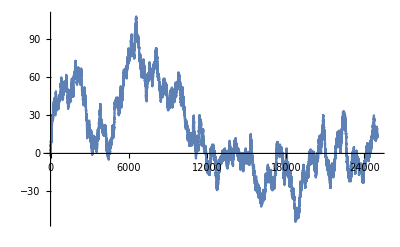

```mathematica
ListLinePlot[Accumulate[RandomChoice[{-1,0,1},{25000}]]]
```

Same but overlaying several random walks.

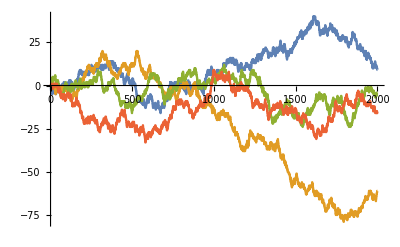

```mathematica
ListStepPlot[Table[Accumulate[RandomChoice[{-1,0,1},{2000}]],{4}]]
```

## Exercises

1. Determine if each of the following are atomic expressions. If the expression is not atomic, find its head.

```mathematica
AtomQ[8/5]
```

True

```mathematica
AtomQ[8/5+x]
Head[8/5+x]
```

False

Plus

```mathematica
AtomQ[{{a,b},{c,d}}]
Head[{{a,b},{c,d}}]
```

False

List

```mathematica
AtomQ["8/5+x"]
```

True

2. Give the full (internal) form of the expression a (b + c).

```mathematica
FullForm[a (b+c)]
```

Times[a,Plus[b,c]]

3. What is the traditional representation of Times [a, Power [Plus[b, c], –1]].

```mathematica
Times [a, Power [Plus[b, c], –1]]
```

a (b+c)^–

4. What is the part specification of the symbol b in the expression a x2 + b x + c?

```mathematica
Part[a x2+b x+c,2]
```

b x

5. What will be the result of evaluating each of the following? Use FullForm on the expressions to help you understand their structures.

```mathematica
FullForm[((x^2+y) z/w)[[2,1,2]]]
```

2

```mathematica
FullForm[(a/b)[[2,2]]]
```

-1

6. Use Level to find all the factors in the following expression. Then find all the terms inside the parentheses of the output.

```mathematica
LegendreP[5,x]
```

1/8 (15 x-70 x^3+63 x^5)

```mathematica
Level[%23[[2]],{2}]
```

{15,x,-70,x^3,63,x^5}

7. Explain why the following expression returns an integer instead of displaying the internal representation of the fraction.

8. Modify the code for the one-dimensional random walk in this section to create two-dimensional random walks.

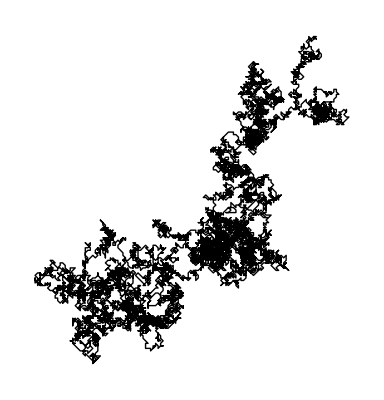

```mathematica
Graphics[Line[Accumulate[RandomChoice[Tuples[{0,1,-1},2],{10000}]]]]
```

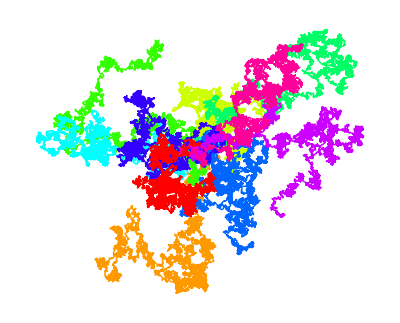

```mathematica
Graphics[Table[{Hue[i/10],Line[Accumulate[RandomChoice[Tuples[{0,1,-1},2],{10000}]]]},{i,1,10}]
]
```